## Kapitola 4 - Přístupy k učení dopředné sítě

Demonstrace použití různých způsobů učení dopředné sítě.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dokumenty\ŠKOLA\ČVUT\BP\BP_Neuron

```mathematica
data=Import["iris.data"];
```

### Načtení dat z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako při načítání ze souboru, jen načtena přímo z internetu.

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Provedeme předzpracování dat pomocí stejného postupu, jaký je popsán v kapitole “Dopředná síť a Iris data”.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

Narozdíl od předchozího notebooku si data rozdělíme na trénovací a testovací množinu. Na trénovací množině budeme síť učit a na testovací množině budeme vyhodnocovat její úspěšnost.
Provedeme náhodné rozdělení dat v poměru 30% testovací a 70% trénovací.

```mathematica
testPercent=30;(*procent pro testovaci data*)
inDataDimension=4;(*dimenze vstupnich dat*)
classes=3;(*pocet trid v datech*)
completeData = Join[inData, outData, 2];
completeData = RandomSample[completeData];
vectors=Dimensions[completeData][[1]];
testData = completeData[[1;;IntegerPart[vectors*testPercent/100]]];
trainData = completeData[[IntegerPart[vectors*testPercent/100]+1;;vectors]];
```

Podívejme se kolik máme trénovacích a kolik testovacích vektorů.

```mathematica
Dimensions[trainData][[1]]
Dimensions[testData][[1]]
```

105

45

Nyní ještě rozdělíme trénovací data na učící a validační množinu, v poměru 70% učicí data a 30% validační data. Na učících datech budeme síť učit a na validačních datech budeme kontrolovat zda se na nich klasifikace zlepšuje. Pokud by se výsledky sítě na validačních datech začaly zhoršovat, přerusíme učení sítě. Tím zabráníme jejímu přeučení (přílišnému přizpůsobení se trénovacím datům).

```mathematica
validatePercent = 30;
vectors2=Dimensions[trainData][[1]];
validationData =  trainData[[1;;IntegerPart[vectors2*validatePercent/100]]];
learnData = trainData[[IntegerPart[vectors2*validatePercent/100]+1;;vectors2]];
```

Rozdělíme si každou vytvořenou množinu dat na vstupní a výstupní část.

```mathematica
testDataIn= testData[[All,1;;inDataDimension]];(*vstupni parametry 1 až 4*)
testDataOut= testData[[All,inDataDimension+1;;inDataDimension+classes]];(*vystupni zakodovane parametry 5 až 7*)
trainDataIn= trainData[[All,1;;inDataDimension]];
trainDataOut= trainData[[All,inDataDimension+1;;inDataDimension+classes]];
validationDataIn= validationData[[All,1;;inDataDimension]];
validationDataOut= validationData[[All,inDataDimension+1;;inDataDimension+classes]];
learnDataIn= learnData[[All,1;;inDataDimension]];
learnDataOut= learnData[[All,inDataDimension+1;;inDataDimension+classes]];
```

Nyní máme připraveny data k učení sítě.

## Výběr a naučení neuronové sítě

Protože nevíme přesně kolik neuronů v síti bude ideální a tipovat by bylo riskantní, použijeme křížovou validaci (podrobněji popsána v samostatné kapitole), která nám určí jaká z předložených sítí podává nejlepší výsledky. Vytvoříme tedy užší výběr tří sítí a ty budeme testovat pomocí křížové validace. Obecně se křížová validace používá k nastavení nejlepších parametrů algoritmu (např. počet neuronů), zde tedy k zjištění struktury sítě.

```mathematica
net1=InitializeRBFNet[inData,outData,1];
net2=InitializeRBFNet[inData,outData,3,Neuron->Sigmoid];
net3=InitializeRBFNet[inData,outData,6,Neuron->Exp];
```

Zavedeme si funkci crossvalidate, jíž dáme jako parametry síť, vstupní data, výstupní data a počet foldů. Funkci je potom možné spustit příkazem crossvalidate[parametry]. Funkce vrací seznam výsledků sítě pro jednotlivé foldy.

```mathematica
crossvalidate[yourNet_,yourInData_,yourOutData_,yourFolds_]:=(Off[NeuralFit::StoppedSearch];
yourVectors = Take[Dimensions[yourInData], 1];
inDataDimensions=Take[Dimensions[yourInData],-1];
outDataDimensions=Take[Dimensions[yourOutData],-1];
yourVectorsInFold = IntegerPart[yourVectors/yourFolds];
yourCompleteData = Join[yourInData, yourOutData, 2];
yourCompleteData = RandomSample[yourCompleteData];
yourBest = 1;
yourWorst = 0;
yourSum = 0;
yourResults={};
For[i = 1, i <= yourFolds, i++,(*kod jednoho kola krossvalidace*)
 yourValidationData = yourCompleteData[[1 + (i - 1)*yourVectorsInFold[[1]] ;; i*yourVectorsInFold[[1]]]];
 yourLearnData = Drop[yourCompleteData, {1 + (i - 1)*yourVectorsInFold[[1]], i*yourVectorsInFold[[1]]}];
 yourValidationDataIn = yourValidationData[[All, 1 ;; inDataDimensions[[1]]]]; yourValidationDataOut = yourValidationData[[All, inDataDimensions[[1]]+1 ;; inDataDimensions[[1]]+outDataDimensions[[1]]]];
 yourLearnDataIn = yourLearnData[[All, 1 ;; inDataDimensions[[1]]]];
 yourLearnDataOut = yourLearnData[[All, inDataDimensions[[1]]+1 ;; inDataDimensions[[1]]+outDataDimensions[[1]]]];
 {netX, record} = NeuralFit[yourNet, yourLearnDataIn, yourLearnDataOut, yourValidationDataIn, yourValidationDataOut, CriterionLog -> False, CriterionPlot -> False];
 current = Take[CriterionValidationValues /. record[[2]], -1];
 If[current[[1]] < yourBest, yourBest = current[[1]], yourBest = yourBest];
 If[current[[1]] > yourWorst, yourWorst = current[[1]], yourWorst = yourWorst];
 yourSum = yourSum + current;
AppendTo[yourResults,current[[1]]];
x=x+1;
 (*Print[i ". fold = ", current[[1]]];*)(*odkomentujte pokud chcete vypsat vysledek pro kazdy fold*)
 ];
Return[yourResults];
)
```

Pomocí funkce crossvalidate provedeme křížovou validaci našich třech sítí a výsledky, pro snadné porovnání, zobrazíme do jednoho grafu.

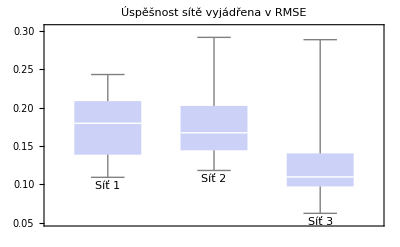

```mathematica
folds=10;
x=0;
Monitor[
g1=crossvalidate[net1,trainDataIn,trainDataOut,folds];
g2=crossvalidate[net2,trainDataIn,trainDataOut,folds];
g3=crossvalidate[net3,trainDataIn,trainDataOut,folds];
BoxWhiskerChart[{g1,g2,g3},PlotLabel->"Úspěšnost sítě vyjádřena v RMSE", ChartLabels->Placed[{"Síť 1", "Síť 2", "Síť 3"},Below]],ProgressIndicator[Dynamic[x],{0,3*folds}]]
```

Z grafu je vidět, že sítě podávají na těchto datech obdobné výkony, můžeme tedy vybrat libovolnou z nich. Vybereme tedy síť 2.

```mathematica
bestNet= InitializeRBFNet[inData,outData,3,Neuron->Sigmoid];
```

Naučíme tuto síť na učicích datech (podmnožina trénovacích dat) a její učení přerusíme v okamžiku kdy se její výsledky začnou na validační množině zhoršovat.

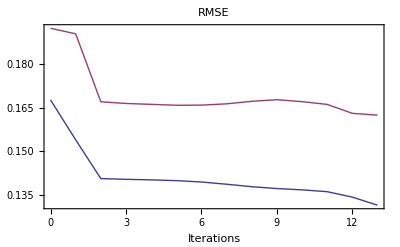

```mathematica
{learnedBestNet, record2} = NeuralFit[bestNet, learnDataIn, learnDataOut, validationDataIn, validationDataOut];
```

Nyní máme naučenou síť, zbývá nám zjistit její skutečnou chybu. Hodnota RMSE, která nám reprezentuje chybovost sítě během učení, není pro člověka tak snadno uchopitelná jako hodnota úspěšnosti v procentech. Vypočteme si tedy skutečnou chybovost sítě v procentech. K tomu použijeme testovací data. Necháme síť oklasifikovat testovací množinu dat a spočteme kolik procent dat klasifikovala správně.

Zavedeme si funkci percentage, která přijímá jako parametry neuronovou síť, vstupní testovací data, výstupní testovací data a vrací úspěšnost sítě v procentech.

```mathematica
percentage[inNet_,testDatIn_, testDatOut_]:=(
testVectors= Dimensions[testDatIn][[1]];
good=0;(*pocet spravne oklasifikovanych*)
clases={};
For[i=1,i<=testVectors,i++,
class=Round[inNet[testDatIn[[i]]]];
AppendTo[clases,class];
If[class==testDatOut[[i]],good=good+1,good=good];
];
Return[good/testVectors*100];)
```

Použijeme tuto funkci k určení skutečné úspěšnosti naší sítě na testovacích datech.

```mathematica
N[percentage[learnedBestNet,testDataIn,testDataOut],5]
```

93.333

## Jiný způsob učení sítě

Možná si říkáte, že rozdělovat trénovací data na učicí a validační je zbytečné. Následuje tedy ukázka postupu učení sítě jen s trénovací množinou a  její zhodnocení pomocí testovací množiny.

Naučíme stejnou síť jakou jsme učili s validační množinou (i na počátku stejně zinicializovanou), ale naučíme ji na všech trénovacích datech.

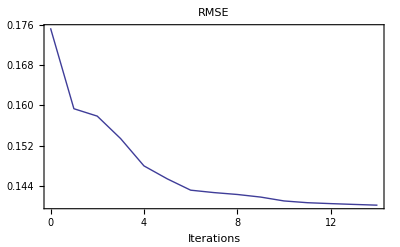

```mathematica
{learnedBestNet2, record2} = NeuralFit[bestNet, trainDataIn, trainDataOut,50];
```

A podíváme se na její skutečnou úspěšnost na testovacích datech.

```mathematica
N[percentage[learnedBestNet2,testDataIn,testDataOut],5]
```

91.111

Pokud si notebook vyhodnotíte několikrát, můžete vypozorovat, že učení s validační množinou podává lepší výsledky než učení na všech trénovacích datech.

Pokud bychom se rozhodli nerozdělovat data ani na testovací a trénovací množinu (viz. předchozí notebook) nemáme již možnost určit skutečnou úsěšnost sítě.

## Prohlášení

Tento text byl vypracován jako součást bakalářské práce Adama Činčury "Demonstrační aplikace pro podporu kurzu neuronových sítí" na FEL ČVUT 2011.